```mathematica
(*Styling of the text*)
st[text_]:=Style[text,Directive[Large,FontFamily->"Linux Libertine Display"]];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

## Import numerical data

```mathematica
(* import τ as a function of q *)
τq1=Import[NotebookDirectory[]<>"data/tauqpsi_rho_1.dat"];
τq09=Import[NotebookDirectory[]<>"data/tauqpsi_rho_09.dat"];
τq08=Import[NotebookDirectory[]<>"data/tauqpsi_rho_08.dat"];
τq07=Import[NotebookDirectory[]<>"data/tauqpsi_rho_07.dat"];
τq06=Import[NotebookDirectory[]<>"data/tauqpsi_rho_06.dat"];
τq05=Import[NotebookDirectory[]<>"data/tauqpsi_rho_05.dat"];
τq04=Import[NotebookDirectory[]<>"data/tauqpsi_rho_04.dat"];
τq03=Import[NotebookDirectory[]<>"data/tauqpsi_rho_03.dat"];
τq02=Import[NotebookDirectory[]<>"data/tauqpsi_rho_02.dat"];
τq01=Import[NotebookDirectory[]<>"data/tauqpsi_rho_01.dat"];
```

```mathematica
τs={τq1,τq09,τq08,τq07,τq06,τq05,τq04,τq03,τq02,τq01};
```

## Legendre transform of τ_q ⟶ f-α graph

```mathematica
legendre[τq_]:=Block[{τinterp,α},
τinterp=Interpolation[τq,InterpolationOrder->10];
α[q_]:=τinterp'[q];
{α[q],q α[q]-τinterp[q]}
]
```

```mathematica
fαs=legendre/@τs;
```

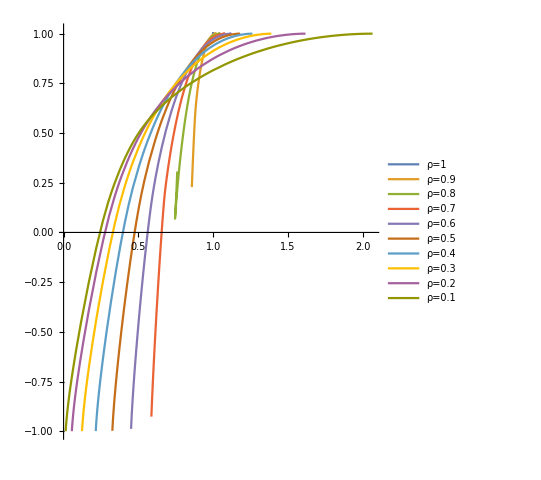

```mathematica
ParametricPlot[fαs,{q,0,20},AspectRatio->1.2,PlotRange->All,PlotLegends->("ρ="<>ToString[#]&/@{1,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1})]
```

## Theoretical implicit equation for τ_q, f-α

```mathematica
ω=(√5-1)/2//N;
(* interference factor *)
gam[ρ_,q_]:=1/(1+ρ^q);
(* molecular and atomic renormalization factors *)
lambp[ρ_]:=((1+gam[ρ,1.] ρ^2-√(1+(gam[ρ,1.] ρ^2)^2))/(2gam[ρ,1.] ρ^2))^-1;
barlambp[ρ_]:=((√((1+ρ^2)^4+4 ρ^4)-(1+ρ^2)^2)/(2 ρ^4))^-1;
(* q-weights for molecular and atomic levels *)
Cm[q_,τq_,ρ_]:=(2+(3-2ω)gam[ρ,q] ρ^(2q))ω^(-2τq)+gam[ρ,q] ρ^(2q)(ω^3/barlambp[ρ]^q ω^(-5τq)-(4 ω^2)/lambp[ρ]^q ω^(-4τq));
Ca[q_,τq_,ρ_]:=(1+2 ρ^(2q)+(3-2ω)ρ^(4q))ω^(-3τq)+ρ^(4q)(ω^3/barlambp[ρ]^q ω^(-6τq)-(4 ω^2)/lambp[ρ]^q ω^(-5τq));
(* implicit equation for the fractal dimensions *)
eq[q_,τq_,ρ_]:=(2 ω^2)/lambp[ρ]^q Cm[q,τq,ρ]+ω^3/barlambp[ρ]^q Ca[q,τq,ρ]-1;
(* find Subscript[τ, q] solving the implicit equation *)
implicitTau[q_,ρ_]:=τ/.FindRoot[eq[q,τ,ρ],{τ,q-1}];
```

## Theoretical prediction for τ_q, f-α

```mathematica
legendreTh[ρ_,qmin_,qmax_]:=Block[{τinterp,α},
τinterp=Interpolation[Table[{q,implicitTau[q,ρ]},{q,qmin,qmax,.01}]];
α[q_]:=τinterp'[q];
{α[q],q α[q]-τinterp[q]}
]
```

```mathematica
fα01th=legendreTh[0.1,-10,20];
```

```mathematica
fα02th=legendreTh[0.2,-10,20];
```

```mathematica
fα03th=legendreTh[0.3,-10,20];
```

```mathematica
fα04th=legendreTh[0.4,-10,20];
```

```mathematica
fα05th=legendreTh[0.5,-10,20];
fα06th=legendreTh[0.6,-10,20];
```

```mathematica
fα01=legendre[τq01];
fα02=legendre[τq02];
fα03=legendre[τq03];
fα05=legendre[τq05];
fα06=legendre[τq06];
```

```mathematica
qr=Range[0,10,0.3];
numdat01=(fα01/.q->#)&/@qr;
numdat02=(fα02/.q->#)&/@qr;
numdat03=(fα03/.q->#)&/@qr;
numdat05=(fα05/.q->#)&/@qr;
numdat06=(fα06/.q->#)&/@qr;
```

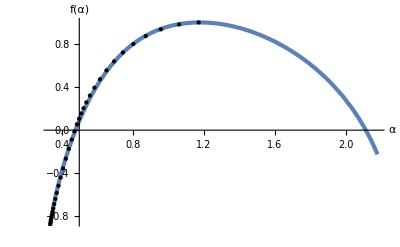

```mathematica
p5=ParametricPlot[fα05th,{q,-4,10},AspectRatio->GoldenRatio^-1,PlotRange->All,AxesLabel->{"α","f(α)"},Epilog->{PointSize[Medium],Point@numdat05},PlotStyle->{AbsoluteThickness[3]}]
```

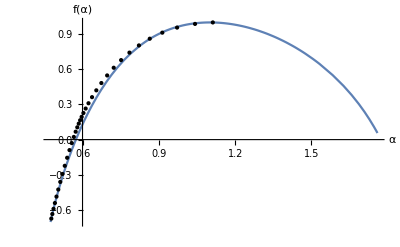

```mathematica
p6=ParametricPlot[fα06th,{q,-4,10},AspectRatio->GoldenRatio^-1,PlotRange->All,AxesLabel->{"α","f(α)"},Epilog->{PointSize[Medium],Point@numdat06}]
```

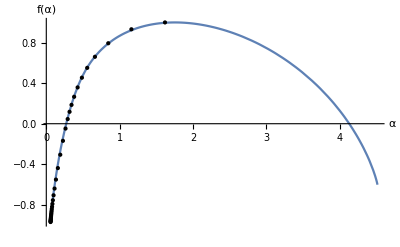

```mathematica
p2=ParametricPlot[fα02th,{q,-4,10},AspectRatio->GoldenRatio^-1,PlotRange->All,AxesLabel->{"α","f(α)"},Epilog->{PointSize[Medium],Point@numdat02}]
```

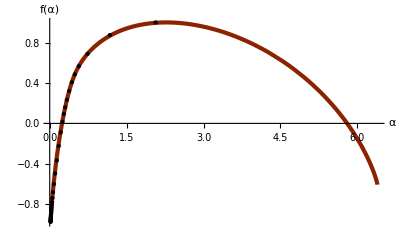

```mathematica
p1=ParametricPlot[fα01th,{q,-6,10},AspectRatio->GoldenRatio^-1,PlotRange->All,AxesLabel->{"α","f(α)"},Epilog->{PointSize[Medium],Point@numdat01},PlotStyle->{AbsoluteThickness[3],comp}]
```

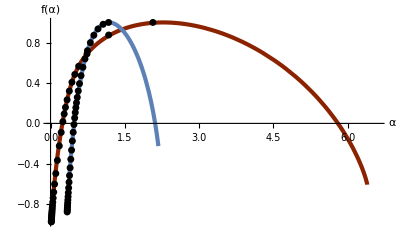

```mathematica
Show[p1,p5,PlotRange->{{0,6.6},Automatic},Epilog->{AbsolutePointSize[5],Point@numdat05,Point@numdat01},AxesStyle->Directive[FontSize->22,FontFamily->"Linux Libertine Display"]]
```

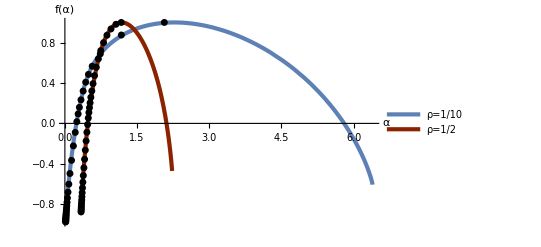

```mathematica
p1=ParametricPlot[{fα01th,fα05th},{q,-6,10},AspectRatio->GoldenRatio^-1,PlotRange->All,AxesLabel->{"α","f(α)"},Epilog->{AbsolutePointSize[5],Point@numdat01,Point@numdat05},PlotStyle->{{AbsoluteThickness[3],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[3],comp}},AxesStyle->Directive[FontSize->22,FontFamily->"Linux Libertine Display"],PlotLegends->st/@{"ρ=1/10","ρ=1/2"}]
```

```mathematica
Export[NotebookDirectory[]<>"falpha_av.pdf",%]
```

/home/nicolas/git/talks/Aperiodic 2015 Prague/falpha_av.pdf

## D_q

```mathematica
τqint05=Interpolation[τq05];
τqint01=Interpolation[τq01];
```

```mathematica
qr=Range[0,20,0.9];
dqnum05={#,τqint05[#]/(#-1)}&/@qr;
dqnum01={#,τqint01[#]/(#-1)}&/@qr;
```

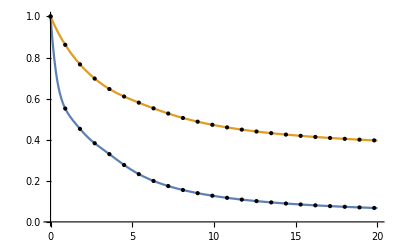

```mathematica
Plot[{τqint01[q]/(q-1),τqint05[q]/(q-1)},{q,0,20},Epilog->{Point@dqnum05,Point@dqnum01}]
```

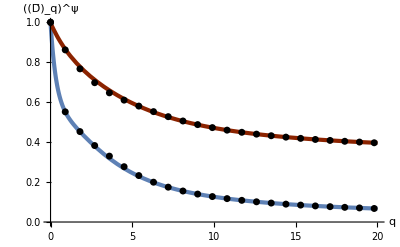

```mathematica
Plot[{(implicitTau[q,0.1]-implicitTau[1,0.1])/(q-1),(implicitTau[q,0.5]-implicitTau[1,0.5])/(q-1)},{q,0,20},Epilog->{AbsolutePointSize[5],Point@dqnum01,Point@dqnum05},PlotStyle->{{AbsoluteThickness[3],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[3],comp}},AxesStyle->Directive[FontSize->22,FontFamily->"Linux Libertine Display"],PlotLegends->None,AxesLabel->{"q","((D̄)_q)^ψ"}]
```

```mathematica
Export[NotebookDirectory[]<>"dq_av.pdf",%]
```

/home/nicolas/git/talks/Aperiodic 2015 Prague/dq_av.pdf